```mathematica
myTicks[lower_,upper_,step_]:=Flatten[Module[{Local=#,LocalTicks},LocalTicks=Log[10,Range[10^(#-1),10^#,(10^#-10^(#-1))/(10-1)]];
Join[{#,""}&/@Most[LocalTicks],{{Last[LocalTicks],Which[Last[LocalTicks]==0,1,Last[LocalTicks]==1,10,True,Power[10,ToString[Last[LocalTicks]]]],{0.03,0}(*longer ticks*)}}]]&/@Range[lower,upper,step],1];
myTicksMajor[lower_,upper_,step_]:=Join[Table[{i,Which[i==0,1,Mod[i,step]==0,Power[10,ToString[i]],True,Null]},{i,lower,upper}]];
```

```mathematica
Mpl=2.4*10^18 
Ms=10^16;
```

2.4×10^18

```mathematica
T=(H Mpl TRH^2)^(1/4)/.{H-> 10,TRH-> 10^7}
```

2.21336×10^8

```mathematica
T=(H Mpl TRH^2)^(1/4)
Tmax=(HI Mpl TRH^2)^(1/4)
TH=Min[10^-2.5 ml √(Ms/HI)]
ma=(ml^(1/2)L^(3/2))/fa Min[1,(L/Max[T,TH])^(7/2)]
L=LI (H/HI)^(2/3)

P=Ms*H/HI
LI=3*10^7(Ms/10^16)^(2/3)
```

39359.8 (H TRH^2)^(1/4)

39359.8 (HI TRH^2)^(1/4)

316228. √(1/HI) ml

1/(fa HI)30000000000 √30 H √ml Min[1,27000000000000000000000000 √30 ((H/HI)^(2/3)/Max[316228. √(1/HI) ml,39359.8 (H TRH^2)^(1/4)])^(7/2)]

10000000 (H/HI)^(2/3)

(10000000000000000 H)/HI

30000000

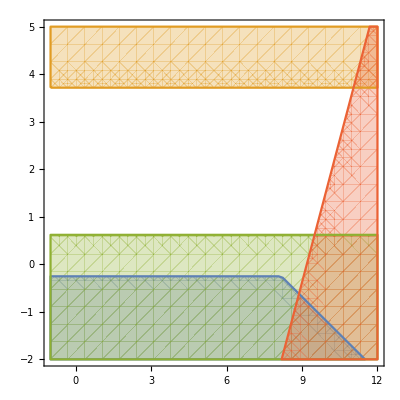

```mathematica
fig=RegionPlot[{((ma/H/.{H-> ((Bμ^(1/2)Ms)/Mpl)})/.{Bμ-> 10^(3*2)/50,fa-> 10^9,ml-> 10^3,HI-> 10^y,TRH-> 10^x,LI-> 3*10^7})>1&&((10^-5*Max[T^2]/P<H)/.{H-> ((Bμ^(1/2)Ms)/Mpl)})/.{Bμ-> 10^(3*2),fa-> 10^9,ml-> 10^3,HI-> 10^y,TRH-> 10^x},

((ml^(1/2)LI^(3/2))/fa<HI)/.{Bμ-> 10^(3*2)/50,fa-> 10^9,ml-> 10^3,HI-> 10^y,TRH-> 10^x},
(ml>HI*Mpl/Ms)/.{Bμ-> 10^(3*2)/50,fa-> 10^9,ml-> 10^3,HI-> 10^y,TRH-> 10^x},
(TRH^4>HI^2*Mpl^2)/.{Bμ-> 10^(3*2)/50,fa-> 10^9,ml-> 10^3,HI-> 10^y,TRH-> 10^x}


},{x,-1,12},{y,-2,5}]
```

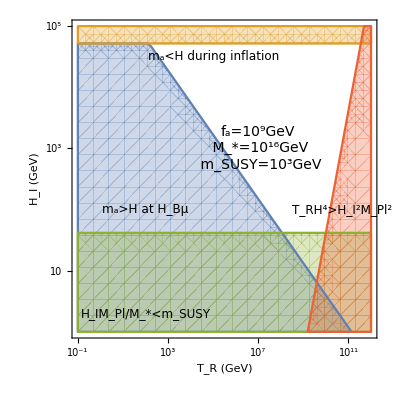

```mathematica
Show[fig,Frame-> {{True,True},{True,True}},
FrameStyle->11,
FrameLabel-> 1{"T_R (GeV)","H_I (GeV)"},AspectRatio->1,
FrameTicks->{{myTicks[-5,15,1],None},{myTicks[-5,15,1],None}},

Epilog-> {
Inset[Style["m_a<H during inflation",FontSize->12],{5,4.5},Automatic,Automatic,{1,0}],
Inset[Style["H_IM_Pl/M_*<m_SUSY",FontSize->12],{2,0.3},Automatic,Automatic,{1,-0.}],
Inset[Style["m_a>H at H_Bμ",FontSize->12],{2,2},Automatic,Automatic,{1,0}],
Inset[Style["T_RH^4>H_I^2M_Pl^2",FontSize->12],{10.7,2},Automatic,Automatic,{1,5}],
Inset[Style["f_a=10^9GeV\n M_*=10^16GeV\n m_SUSY=10^3GeV",FontSize->14],{7,3.},Automatic,Automatic,{1,0}]
}
]
```